```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-70_phon_dos"];
phDOSfiles={"1.total_dos.dat","2.total_dos.dat","3.total_dos.dat","4.total_dos.dat","5.total_dos.dat","6.total_dos.dat","7.total_dos.dat","8.total_dos.dat","9.total_dos.dat","10.total_dos.dat","11.total_dos.dat"};
fren70dos=Table[ReadList[phDOSfiles[[i]],{Number,Number}],{i,1,Length@phDOSfiles}];
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/perf_phon_dos"];
perf=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-1126_phon_dos"];
fren1126=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-129_phon_dos"];
fren129=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-142_phon_dos"];
fren142=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-174_phon_dos"];
fren174=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_17July17/phonon_dos/fren-70_phon_dos"];
fren70=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
```

```mathematica
names={"perf","fren129","fren142","fren70","fren174","fren1126"};
objects={perf,fren129,fren142,fren70,fren174,fren1126};
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850,4.875,4.900};
vols=(alatts*2)^3/64;
```

```mathematica
fren1126Data=Table[Table[Flatten[{fren1126[[j]][[i]][[1]],vols[[j]],fren1126[[j]][[i]][[2]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
fren1126Data2D=Table[Table[Flatten[{fren1126[[j]][[i]][[1]],fren1126[[j]][[i]][[2]]+10*vols[[j]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
data=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]],vols[[j]],objects[[k]][[j]][[i]][[2]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
data2D=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]],objects[[k]][[j]][[i]][[2]]+10*vols[[j]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
```

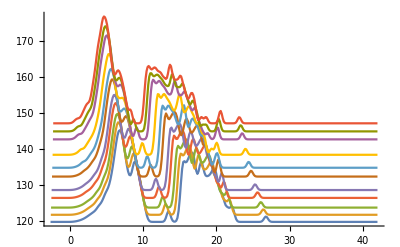

```mathematica
ListPointPlot3D@fren1126Data;
ListLinePlot@fren1126Data2D
```

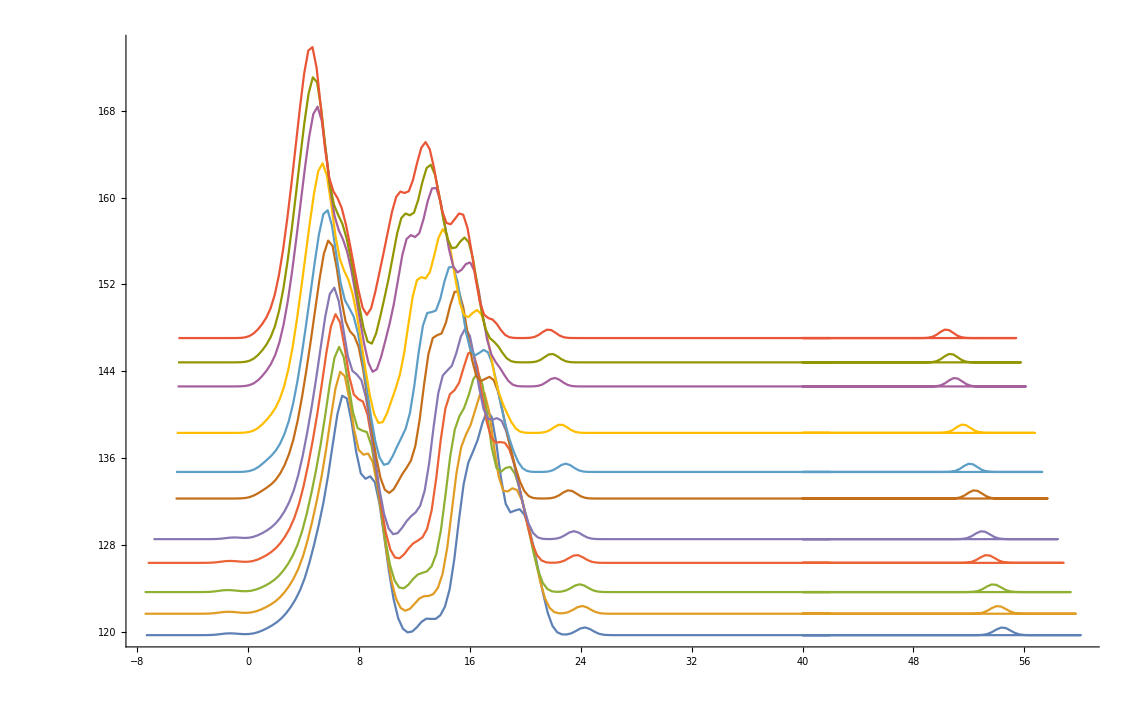

```mathematica
ListLinePlot@data2D[[4]]
```

```mathematica
2
```

#### Plot3d

```mathematica
plotStyle3D={BoxRatios->{1,1,1},FillingStyle->Directive[Thickness[1],Orange,Thin,Opacity[0.1]],Filling->Bottom,PlotTheme->"Scientific",AxesLabel->{Style["ω (THz)",18,Black],Style["Volume \n(Å^3/atom) ",18,Black],Style["DOS ",18,Black]" \n(1/THz)  "},AxesStyle->Directive[18,Black,Thickness[0.004]],Boxed->False,BoxStyle->Directive[Thickness[0.00001],Dashing[0.02]],PlotStyle->Directive[Black,PointSize[0.006]],ImageSize->650,ViewPoint->{-5005,-100000,15}};
ListPointPlot3D[fren1126Data,Evaluate@plotStyle3D]/.Point[a___]:>{Thickness[0.004],Line[a]};
```

#### Plot2D

56

36

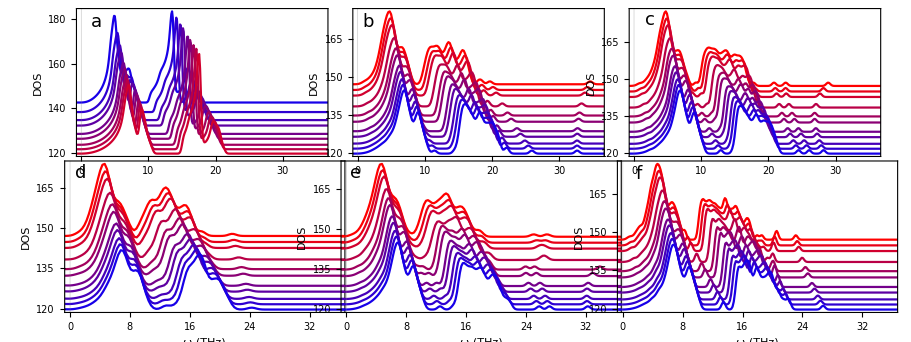

```mathematica
par=36
plotStyle={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,None},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS ",18,Black]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->450,PlotRange->{{0,30},Automatic}};

plotStyle1={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS ",18,Black]},PlotStyle->Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Reverse@Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["a",18,Black],{0.09,0.88}]}};




plotStyle2={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["b",18,Black],{0.113,0.86}]}};
plotStyle3={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["c",18,Black],{0.128,0.88}]}};
plotStyle4={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS ",18,Black]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->390,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["d",18,Black],{0.106,0.87}]}};


plotStyle5={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->390,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["e",18,Black],{0.13,0.88}]}};
plotStyle6={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->390,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["f",18,Black],{0.1,0.87}]}};
plotStyles={plotStyle1,plotStyle2,plotStyle3,plotStyle4,plotStyle5,plotStyle6};

plots=Table[ListLinePlot[Reverse@data2D[[i]],Evaluate@plotStyles[[i]]],{i,1,6}];
gridplot=GraphicsGrid[{plots[[1;;3]],plots[[4;;6]]},Spacings->{-90,-30}]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/phon-dos.pdf",gridplot]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/phon-dos.pdf

```mathematica
Log[1]
```

0

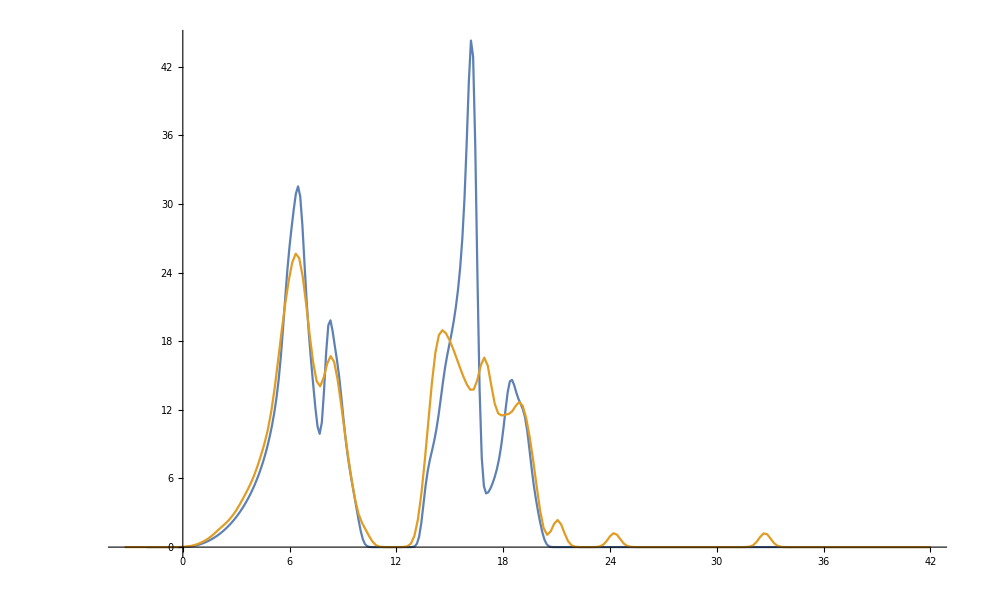

```mathematica
ListLinePlot[{perf[[4]],fren129[[4]]}]
```

```mathematica
pInt=Interpolation[perf[[4]]];
pFren129=Interpolation[fren129[[4]]];
pFren142=Interpolation[fren142[[4]]];
pFren70=Interpolation[fren70[[4]]];
gmean[arg_,min_,max_]:=Exp[Integrate[Log[x]*arg[x],{x,min,max}]/Integrate[arg[x],{x,min,max}]]//N
mean[arg_,min_,max_]:=Integrate[x*arg[x],{x,min,max}]/Integrate[arg[x],{x,min,max}]//N
n[arg_,min_,max_]:=Integrate[arg[x],{x,min,max}]//N
```

```mathematica
ints[[1]];
```

```mathematica
ints=Table[Table[Interpolation[objects[[i]][[j]]],{j,1,objects[[i]]//Length}],{i,1,6}];
```

```mathematica
Integrate[ints[[4]][[4]][x],{x,-3,56}]
```

191.999

```mathematica
gmean[pInt,0,12]
gmean[pFren129,0,12]
```

6.36559

6.25654

```mathematica
gmean[pInt,12,20.7]
gmean[pFren129,12,20.7]
-64Log[gmean[pFren129,0,50]/gmean[pInt,0,35]]
```

16.3824

16.3671

0.394923

```mathematica
gmean[pInt,0,35]
gmean[pFren70,-3,57]
gmean[pFren70,0,57]
```

10.2119

10.0301+0.0513697 ⅈ

10.0688

```mathematica
pFren70
```

InterpolatingFunction[{{-7.25057, 58.817}}, <>]

```mathematica
-64Log[gmean[pFren70,0,57]/gmean[pInt,0,35]]
-64Log[gmean[pFren70*192/191,0,57]/gmean[pInt,0,35]]
```

0.903559

NIntegrate::nlim: x = Null is not a valid limit of integration.

-64 Log[0.0979245 2.71828^(NIntegrate[Log[x] (192 InterpolatingFunction[{{-7.25057, 58.817}}, <>])/191[x],{x,Null,57}]/NIntegrate[(192 InterpolatingFunction[{{-7.25057, 58.817}}, <>])/191[x],{x,Null,57}])]

```mathematica
names
objects;
```

{perf,fren129,fren142,fren70,fren174,fren1126}

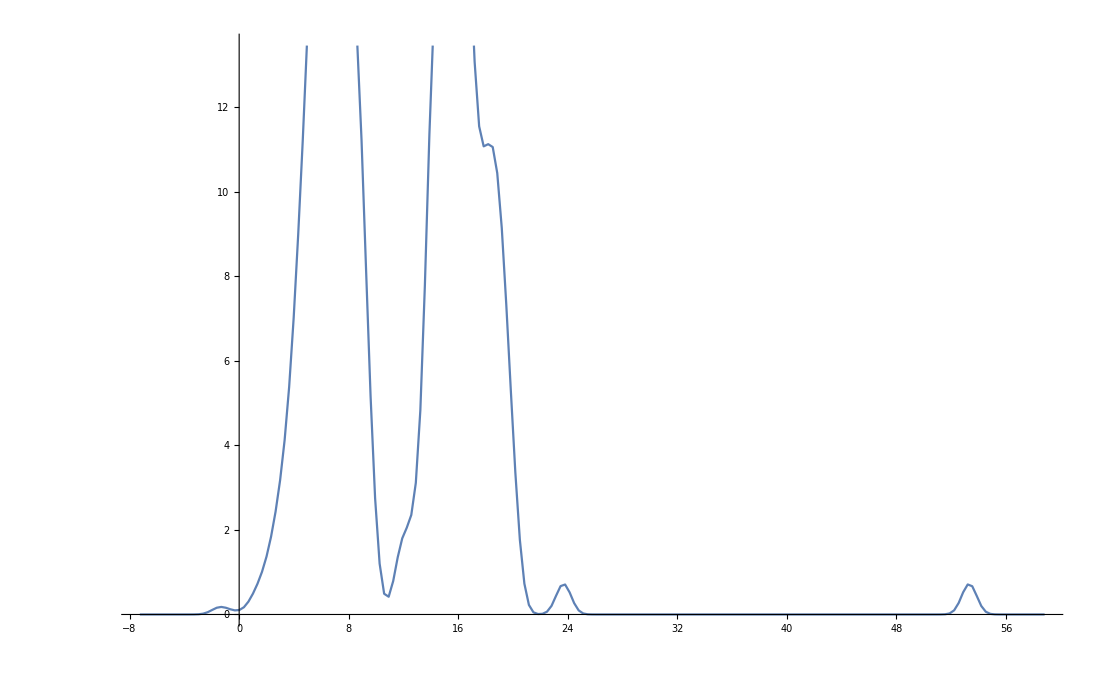

```mathematica
ListLinePlot[ints[[4]][[4]]]
```

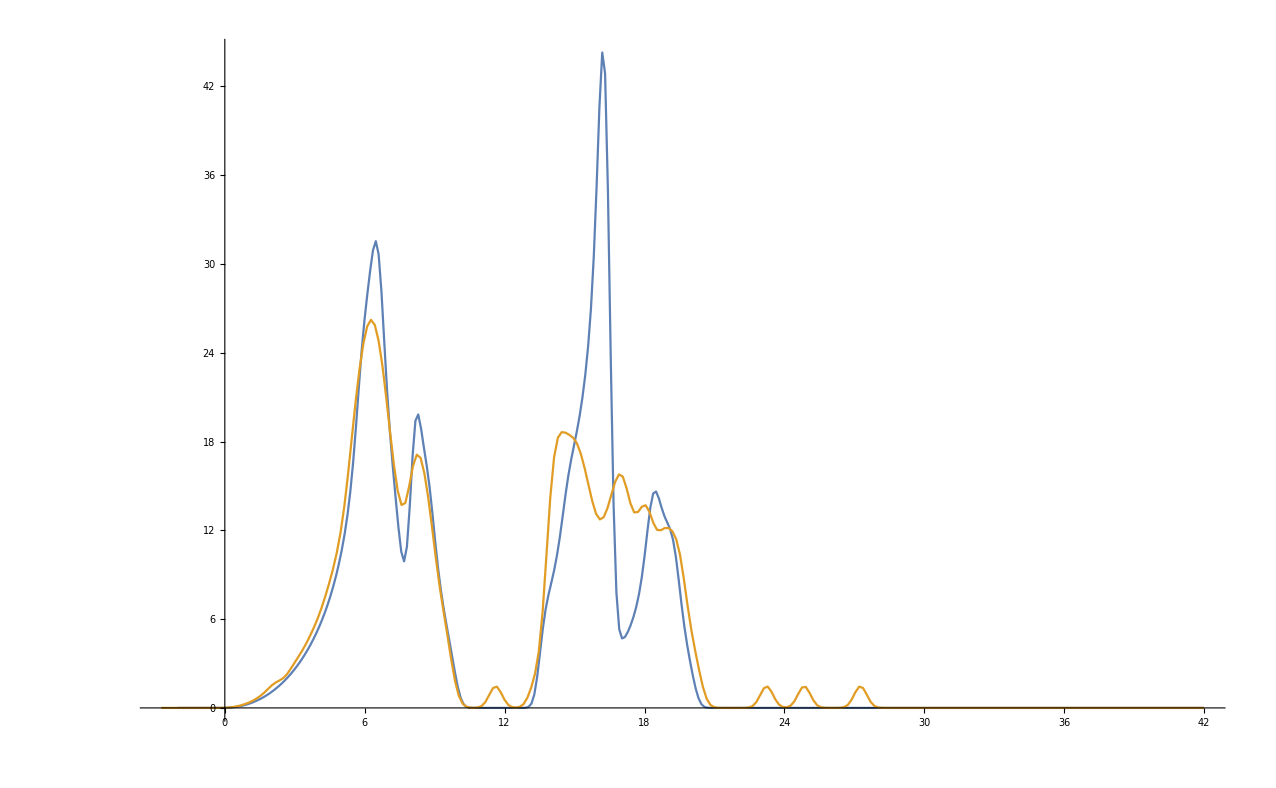

```mathematica
ListLinePlot[Table[ints[[i]][[4]],{i,1,3,2}]]
```

```mathematica
gmean[pInt,12.5,22]
gmean[pFren142,12.5,22]
n[pInt,12.5,22]
n[pFren142,12.5,22]
n[pFren142,12.5,22]/n[pInt,12.5,22]
```

16.3824

16.4672

96.

91.9993

0.958326

```mathematica
n[pInt,0,12.5]
n[pFren142,0,12.5]
n[pInt,0,12.5]/n[pFren142,0,12.5]
```

95.9994

96.999

0.989695

```mathematica
3*32
```

96

```mathematica
deltaS
```

{{1.47851,3.00691,5.12244,6.86683,9.93876},{1.41556,2.86123,4.84095,6.4845,9.33778}}

```mathematica
objects[[1]][[1]][[-1]][[1]]
```

42

```mathematica
objects[[1]]//Dimensions
```

{9,203,2}

```mathematica
objects[[1]][[j]][[-1]][[1]]
```

```mathematica
ints//Dimensions
```

{6,9}

```mathematica
ints//Dimensionsc
objects//Dimensions
```

{6,9}

{6}

```mathematica
nn=Table[Table[n[ints[[j]][[i]],0,objects[[j]][[i]][[-1]][[1]]]/192,{i,1,objects[[j]]//Length}],{j,2,6}]
```

{{0.999987,0.999986,0.999985,0.999984,0.999982,0.999979,0.999976,0.99997,0.999956,0.999944,0.999913},{0.999992,0.999992,0.999992,0.999991,0.999991,0.999989,0.999988,0.999984,0.999976,0.999964,0.999786},{0.993244,0.993116,0.993076,0.993157,0.993512,0.99465,0.994703,0.994696,0.994668,0.994642,0.994597},{0.999988,0.999988,0.999987,0.999986,0.999984,0.99998,0.999974,0.995046,0.994494,0.99418,0.993987},{0.999994,0.999993,0.999993,0.999993,0.999993,0.999992,0.999991,0.999989,0.999983,0.999981,0.999974}}

```mathematica
Table[Join[{names[[j]]},Table[n[ints[[j]][[i]],0,objects[[j]][[i]][[-1]][[1]]]/192,{i,1,objects[[j]]//Length}]],{j,1,6}]//TableForm
```

perf | 0.999997 | 0.999997 | 0.999997 | 0.999997 | 0.999997 | 0.999997 | 0.999997 | 0.999997 | 0.999996 |  | 
fren129 | 0.999987 | 0.999986 | 0.999985 | 0.999984 | 0.999982 | 0.999979 | 0.999976 | 0.99997 | 0.999956 | 0.999944 | 0.999913
fren142 | 0.999992 | 0.999992 | 0.999992 | 0.999991 | 0.999991 | 0.999989 | 0.999988 | 0.999984 | 0.999976 | 0.999964 | 0.999786
fren70 | 0.993244 | 0.993116 | 0.993076 | 0.993157 | 0.993512 | 0.99465 | 0.994703 | 0.994696 | 0.994668 | 0.994642 | 0.994597
fren174 | 0.999988 | 0.999988 | 0.999987 | 0.999986 | 0.999984 | 0.99998 | 0.999974 | 0.995046 | 0.994494 | 0.99418 | 0.993987
fren1126 | 0.999994 | 0.999993 | 0.999993 | 0.999993 | 0.999993 | 0.999992 | 0.999991 | 0.999989 | 0.999983 | 0.999981 | 0.999974

```mathematica
deltaS=Table[Table[-64Log[gmean[ints[[1+j]][[i]],0,objects[[1+j]][[i]][[-1]][[1]]]/(gmean[ints[[1]][[i]],0,objects[[1]][[i]][[-1]][[1]]])],{i,1,9}],{j,1,5}]
```

{{0.675583,0.612586,0.529797,0.393894,0.292943,0.0740912,-0.0710538,-0.302869,-0.604015},{0.511933,0.451886,0.374515,0.240644,0.132171,-0.0820827,-0.231497,-0.468489,-0.794885},{1.16753,1.12795,1.08886,1.0235,1.02636,1.08492,0.956428,0.790816,0.622771},{0.684699,0.638526,0.573538,0.466937,0.388123,0.262104,0.27159,0.35788,0.0090754},{0.656975,0.609787,0.541768,0.418793,0.311557,0.0942619,-0.0549775,-0.302427,-0.657618}}

```mathematica
Transpose[deltaS]
```

{{0.675583,0.511933,1.16753,0.684699,0.656975},{0.612586,0.451886,1.12795,0.638526,0.609787},{0.529797,0.374515,1.08886,0.573538,0.541768},{0.393894,0.240644,1.0235,0.466937,0.418793},{0.292943,0.132171,1.02636,0.388123,0.311557},{0.0740912,-0.0820827,1.08492,0.262104,0.0942619},{-0.0710538,-0.231497,0.956428,0.27159,-0.0549775},{-0.302869,-0.468489,0.790816,0.35788,-0.302427},{-0.604015,-0.794885,0.622771,0.0090754,-0.657618}}

```mathematica
Table[Join[{names[[i+1]]},deltaS[[i]]],{i,1,5}]//TableForm
```

fren129 | 0.675583 | 0.612586 | 0.529797 | 0.393894 | 0.292943 | 0.0740912 | -0.0710538 | -0.302869 | -0.604015
fren142 | 0.511933 | 0.451886 | 0.374515 | 0.240644 | 0.132171 | -0.0820827 | -0.231497 | -0.468489 | -0.794885
fren70 | 1.16753 | 1.12795 | 1.08886 | 1.0235 | 1.02636 | 1.08492 | 0.956428 | 0.790816 | 0.622771
fren174 | 0.684699 | 0.638526 | 0.573538 | 0.466937 | 0.388123 | 0.262104 | 0.27159 | 0.35788 | 0.0090754
fren1126 | 0.656975 | 0.609787 | 0.541768 | 0.418793 | 0.311557 | 0.0942619 | -0.0549775 | -0.302427 | -0.657618

```mathematica
deltaSAt=deltaS/64
```

{{0.010556,0.00957166,0.00827807,0.00615459,0.00457723,0.00115768,-0.00111022,-0.00473232,-0.00943773},{0.00799895,0.00706073,0.0058518,0.00376006,0.00206518,-0.00128254,-0.00361713,-0.00732014,-0.0124201},{0.0182427,0.0176242,0.0170134,0.0159923,0.0160369,0.0169519,0.0149442,0.0123565,0.0097308},{0.0106984,0.00997696,0.00896154,0.00729589,0.00606442,0.00409537,0.00424359,0.00559187,0.000141803},{0.0102652,0.00952792,0.00846513,0.00654365,0.00486808,0.00147284,-0.000859023,-0.00472541,-0.0102753}}

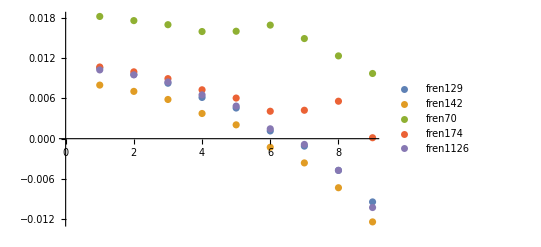

```mathematica
ListPlot[deltaSAt,PlotLegends->names[[2;;-1]]]
```

```mathematica
D[D[10x^8*7,x],x]
D[D[10x^8,x],x]*7
```

3920 x^6

3920 x^6